```mathematica
Limit[(4(1+h)-(1+h)^2-3)/h,{h->0}]
```

{2}

```mathematica
Limit[(4x-x^2-3)/(x-1),{x->1}]
```

{2}

```mathematica
Limit[((x-1)/(x-2)-2)/(x-3),{x->3}]
```

{-1}

```mathematica
f[t_]:=10t-1.86t^2
f'[a]
```

10-3.72 a

```mathematica
Solve[f[t]==0,t]
```

{{t→0.+0. ⅈ},{t→5.37634}}

```mathematica
f'[5.37634]
```

-9.99998

```mathematica
f[x_]:=Sqrt[3x+10]
f'[x]//TraditionalForm
```

3/(2 √(3 x+10))

```mathematica
Solve[1/2 ==(y-1)/(x-1),y]
```

{{y→(1+x)/2}}

```mathematica
f[x_]:=5000+10x+0.05x^2
f[{100,101,105}]
r[a_,b_]:=(f[a]-f[b])/(a-b)
r[100,101]
f'[100]
```

{6500.,6520.05,6601.25}

20.05

20.

x^2-4 x+3

x^2-4 x+3

x^3/3-2 x^2+3 x

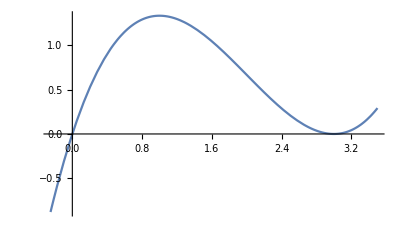

```mathematica
p=InterpolatingPolynomial[{{0,3},{1,0},{2,-1}},x]//Expand//TraditionalForm
f[x_]=p/.x->x
Integrate[x^2-4x+3,x]//TraditionalForm
g[x_]:=x^3/3-2 x^2+3 x
Plot[g[x],{x,-0.25,3.5},AspectRatio->Automatic]
```

```mathematica
f[x]
```

x^2-4 x+3

```mathematica
g[2]
```

Integrate::ilim: Invalid integration variable or limit(s) in 2.

∫-1ⅆ2